```mathematica
v := {{0,0},{1/7,0}, {2/7,1/21},{3/7,1/5},{4/7,18/35},{5/7,19/21},{6/7, 1},{1,1}};
v2 := {{0,0},{1/7,0}, {2/7,1/21},{3/7,2/35},{4/7,2/35},{5/7,19/21},{6/7, 1},{1,1}};
v3 := {{0,0},{1/7,0}, {2/7,1/21},{3/7,31/35},{4/7,31/35},{5/7,19/21},{6/7, 1},{1,1}};
```

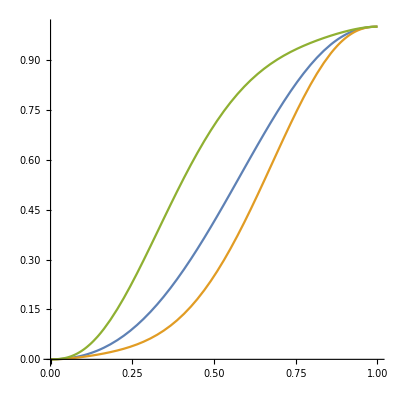

```mathematica
ParametricPlot[{BezierFunction[v][x],BezierFunction[v2][x], BezierFunction[v3][x]},{x,0,1}]
```

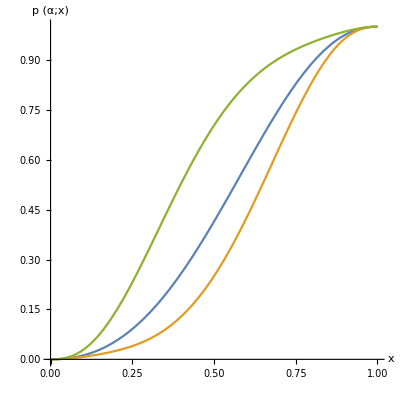

```mathematica
Show[%10,AxesLabel->{HoldForm[x],HoldForm[p (α;x)]},PlotLabel->None,LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
Export["/Users/eubank/reliability/doc/Papers/curves.pdf",%13,"PDF"]
```

/Users/eubank/reliability/doc/Papers/curves.pdf

```mathematica
Export["/Users/eubank/reliability/doc/Papers/curves.pdf",%10,"PDF"]
```

/Users/eubank/reliability/doc/Papers/curves.pdf

```mathematica
Export["/Users/eubank/reliability/doc/Papers/curves.pdf",%10,"PDF"]
```

/Users/eubank/reliability/doc/Papers/curves.pdf

```mathematica
h[w_,w1_,w6_] := w^2(2-w^2)(1+w((1/w1) - 1/w6)) - w;
```

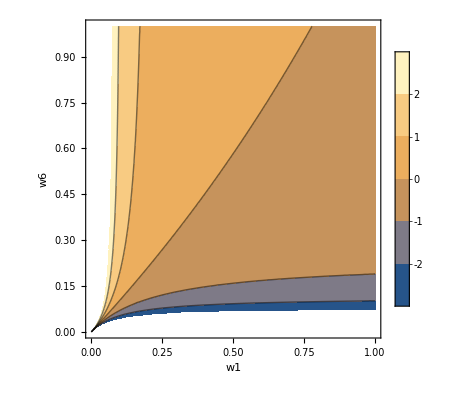

```mathematica
ContourPlot[h[0.5,w1,w6],{w1,0,1},{w6,0,1},PlotLegends->Automatic,AxesLabel->{"w1","w6"}]
```